```mathematica
(* ==============================================================================*)(*SENSITIVITY ANALYSIS FOR PHYTOPLANKTON GROWTH MODELS*)(* ==============================================================================*)
```

```mathematica
(*Run this first to set up the directories for inputting parameters and exporting a PDF*)
basePath=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"output"}]
paramsDir=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data"}]
```

```mathematica
(*Define a plotting function for consistent frames*)
ClearAll[MakeSensitivityPlot];
MakeSensitivityPlot[expr_,{xVar_,xMin_,xMax_},title_,xLabel_]:=
Plot[expr,{xVar,xMin,xMax},
PlotRange->All,
PlotRangePadding->{Scaled[0.02],Scaled[0.08]},
Frame->True,
Axes->False,
FrameLabel->{{"Sensitivity",None},{xLabel,title}},
PlotStyle->Directive[Black,Thickness[0.003]],
GridLines->{None,{0}},
GridLinesStyle->Directive[Black,Dashed,AbsoluteThickness[1.5]],
FrameStyle->Directive[Black,Thickness[0.002]],
BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontColor->Black},
ImagePadding->{{85,20},{60,20}},
ImageSize->400,
Background->White]
```

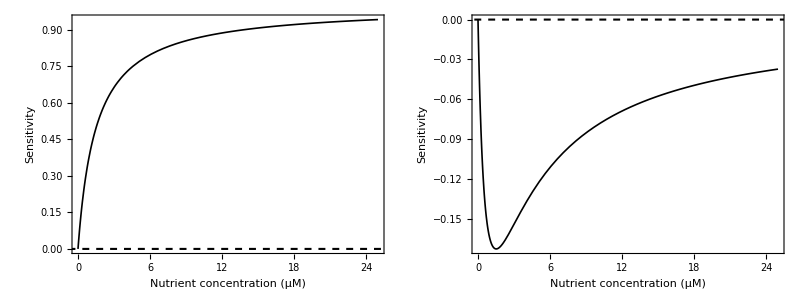
-Graphics-Sensitivity of Monod parameters

```mathematica
(* ==============================================================================*)
(*1. MONOD FUNCTION (NUTRIENTS)*)
(* ==============================================================================*)
monodData=Import[FileNameJoin[{paramsDir,"nutrient_MBD_params.csv"}],"Data"];
mumaxM=monodData[[2,1]];
kM=monodData[[2,2]];

monodExpr=(mumax*x)/(x+k);
dMumaxMonod=D[monodExpr,mumax]/. {mumax->mumaxM,k->kM};
dKMonod=D[monodExpr,k]/. {mumax->mumaxM,k->kM};

xLabelMonod=Row[{"Nutrient concentration (μM)"}];
pM1=MakeSensitivityPlot[dMumaxMonod,{x,0,25},Subscript["μ","max"],xLabelMonod];
pM2=MakeSensitivityPlot[dKMonod,{x,0,25},"K",xLabelMonod];

plotMonod=Style[Labeled[Grid[{{pM1,pM2}},Spacings->{2,0}],Style["Sensitivity of Monod parameters",24],Top],
Background->White]
Export[FileNameJoin[{basePath,"Sensitivity_Monod_Nutrients.pdf"}],plotMonod];
```

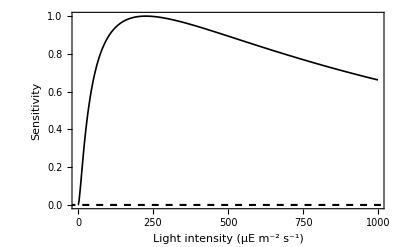
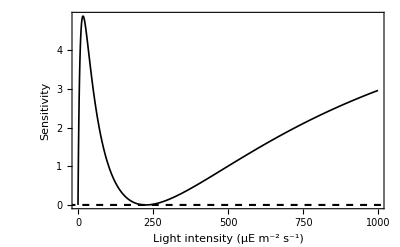
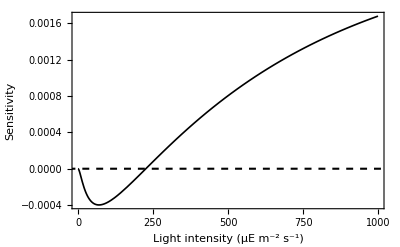
-Graphics- | -Graphics-
-Graphics- | Sensitivity of Eilers-Peeters parameters

```mathematica
(* ==============================================================================*)
(*2. EILERS-PEETERS FUNCTION (LIGHT)*)
(* ==============================================================================*)
lightData=Import[FileNameJoin[{paramsDir,"light_MBD_params.csv"}],"Data"];
mumaxL=lightData[[2,1]];alphaL=lightData[[2,2]];ioptL=lightData[[2,3]];

epExpr=(mumax*light)/(((mumax/(alpha*iopt^2))*light^2)+((1-(2*mumax)/(alpha*iopt))*light)+(mumax/alpha));
dMumaxEP=D[epExpr,mumax]/. {mumax->mumaxL,alpha->alphaL,iopt->ioptL};
dAlphaEP=D[epExpr,alpha]/. {mumax->mumaxL,alpha->alphaL,iopt->ioptL};
dIoptEP=D[epExpr,iopt]/. {mumax->mumaxL,alpha->alphaL,iopt->ioptL};

xLabelLight=Row[{"Light intensity (μE ",Superscript["m","-2"]," ",Superscript["s","-1"],")"}];

pL1=MakeSensitivityPlot[dMumaxEP,{light,0,1000},Subscript["μ","max"],xLabelLight];
pL2=MakeSensitivityPlot[dAlphaEP,{light,0,1000},"α",xLabelLight];
pL3=MakeSensitivityPlot[dIoptEP,{light,0,1000},Subscript["I","opt"],xLabelLight];

plotLight=Style[Labeled[Grid[{{pL1,pL2},{pL3}},Spacings->{2,0}],Style["Sensitivity of Eilers-Peeters parameters",24],Top],
Background->White]
Export[FileNameJoin[{basePath,"Sensitivity_EilersPeeters_Light.pdf"}],plotLight];
```

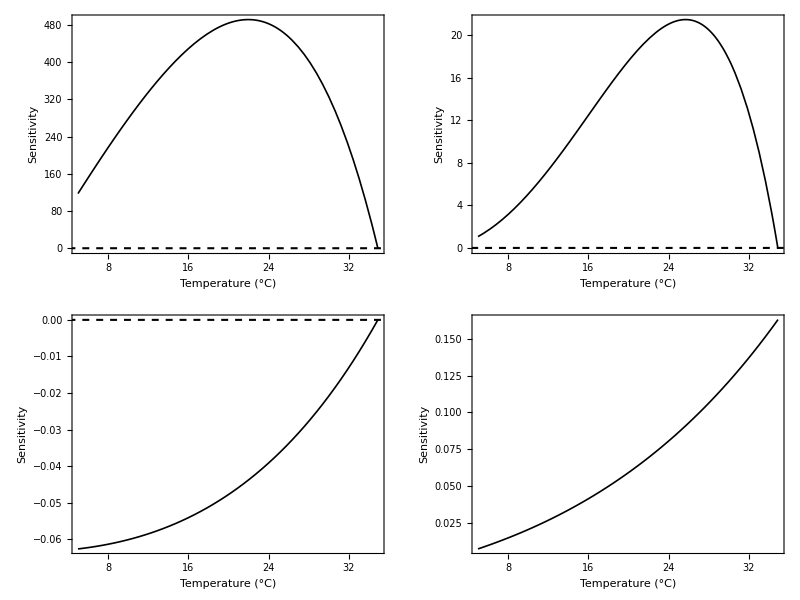
-Graphics-Sensitivity of Norberg parameters

```mathematica
(* ==============================================================================*)
(*3. NORBERG FUNCTION (TEMPERATURE)*)
(* ==============================================================================*)
tempData=Import[FileNameJoin[{paramsDir,"temperature_MBD_params.csv"}],"Data"];
aM=tempData[[2,1]];bM=tempData[[2,2]];tmaxM=tempData[[2,3]];tminM=tempData[[2,4]];

norbergExpr=(a*Exp[b*temp])*(tmax-temp)*(temp-tmin);
dA=D[norbergExpr,a]/. {a->aM,b->bM,tmax->tmaxM,tmin->tminM};
dB=D[norbergExpr,b]/. {a->aM,b->bM,tmax->tmaxM,tmin->tminM};
dTmax=D[norbergExpr,tmax]/. {a->aM,b->bM,tmax->tmaxM,tmin->tminM};
dTmin=D[norbergExpr,tmin]/. {a->aM,b->bM,tmax->tmaxM,tmin->tminM};

xLabelTemp=Row[{"Temperature (°C)"}];

pT1=MakeSensitivityPlot[dA,{temp,5,34.9},"a",xLabelTemp];
pT2=MakeSensitivityPlot[dB,{temp,5,34.9},"b",xLabelTemp];
pT3=MakeSensitivityPlot[dTmax,{temp,5,34.9},Subscript["T","max"],xLabelTemp];
(*Note that this curve can change its shape within the design shape under some parameter combinations*)
(*See Section 6, SI for details*)
pT4=MakeSensitivityPlot[dTmin,{temp,5,34.9},Subscript["T","min"],xLabelTemp];

plotTemp=Style[Labeled[Grid[{{pT1,pT2},{pT4,pT3}},Spacings->{2,2}],Style["Sensitivity of Norberg parameters",24],Top],Background->White]
Export[FileNameJoin[{basePath,"Sensitivity_Norberg_Temperature.pdf"}],plotTemp];
```

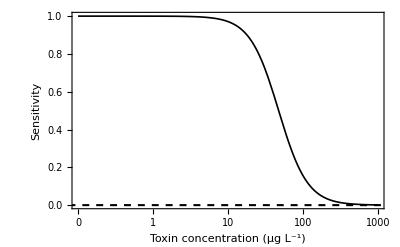
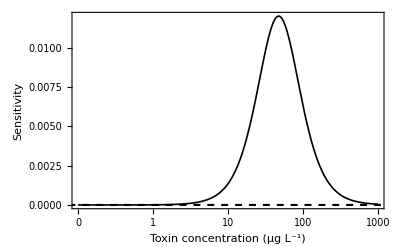
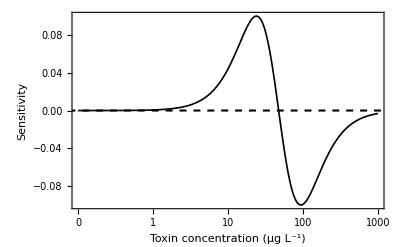
-Graphics- | -Graphics-
-Graphics- | Sensitivity of dose-response parameters

```mathematica
(* ==============================================================================*)
(*4. LOG-LOGISTIC FUNCTION (TOXINS)*)
(* ==============================================================================*)
(*Note that this is on a pseudo-log scale*)
(*1. Define the R pseudo-log transformation mathematically*)
sigma=0.1;
base=10;
psLog[x_]:=ArcSinh[x/(2*sigma)]/Log[base];
invPsLog[y_]:=Sinh[y*Log[base]]*(2*sigma);

(*2. Define a duplicate plotting function that applies the custom scale*)
MakeSensitivityPlotPseudoLog[expr_,{xVar_,xMin_,xMax_},title_,xLabel_]:=
Plot[expr,{xVar,xMin,xMax},
ScalingFunctions->{{psLog,invPsLog},None},FrameTicks->{{Automatic,None},{{{0,"0"},{1,"1"},{10,"10"},{100,"100"},{1000,"1000"}},None}},
PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.08]},
Frame->True,
Axes->False,
FrameLabel->{{"Sensitivity",None},{xLabel,title}},
PlotStyle->Directive[Black,Thickness[0.003]],
GridLines->{None,{0}},
GridLinesStyle->Directive[Black,Dashed,AbsoluteThickness[1.5]],
FrameStyle->Directive[Black,Thickness[0.002]],BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontColor->Black},
ImagePadding->{{85,20},{60,20}},
ImageSize->400,
Background->White]

(*3. Data imports and derivatives*)
toxinData=Import[FileNameJoin[{paramsDir,"toxin_MBD_params.csv"}],"Data"];
dM=toxinData[[2,1]];eM=toxinData[[2,2]];hM=toxinData[[2,3]];

drExpr=d/(1+(x/e)^h);
dD=D[drExpr,d]/. {d->dM,e->eM,h->hM};
dH=D[drExpr,h]/. {d->dM,e->eM,h->hM};
dE=D[drExpr,e]/. {d->dM,e->eM,h->hM};

xLabelToxin=Row[{"Toxin concentration (μg ",Superscript["L","-1"],")"}];

(*4. Call the new function*)
pDR1=MakeSensitivityPlotPseudoLog[dD,{x,0,1000},Subscript["μ","max"],xLabelToxin];
pDR2=MakeSensitivityPlotPseudoLog[dH,{x,0,1000},"h",xLabelToxin];
pDR3=MakeSensitivityPlotPseudoLog[dE,{x,0,1000},"e",xLabelToxin];

(*5. Combine and export*)
plotDR=Style[Labeled[Grid[{{pDR1,pDR3},{pDR2}},Spacings->{2,0}],Style["Sensitivity of dose-response parameters",24],Top],Background->White]
Export[FileNameJoin[{basePath,"Sensitivity_DoseResponse_Toxins.pdf"}],plotDR];
```